```mathematica
Eigenvalues[({{x y, 2}, {2, -(x^2+y^2)}})]//MatrixForm
```

(1/2 (-x^2+x y-y^2-√(16+x^4+2 x^3 y+3 x^2 y^2+2 x y^3+y^4))
1/2 (-x^2+x y-y^2+√(16+x^4+2 x^3 y+3 x^2 y^2+2 x y^3+y^4)))

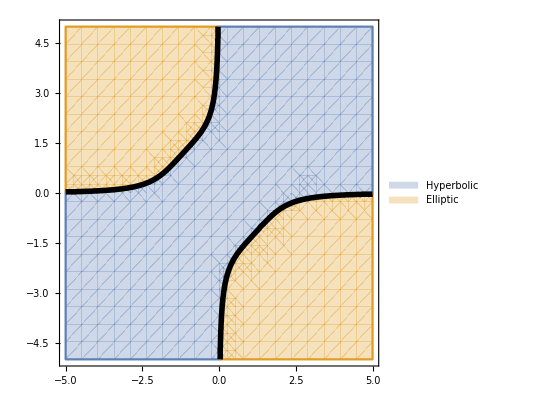

```mathematica
Show[{
RegionPlot[{1/2 (-x^2+x y-y^2+√(16+(x^2+x y+y^2)^2))>0,1/2 (-x^2+x y-y^2+√(16+(x^2+x y+y^2)^2))<0},{x,-5,5},{y,-5,5},
PlotLegends->{"Hyperbolic","Elliptic"}],
ContourPlot[x y(x^2+y^2)+4==0,{x,-5,5},{y,-5,5},
PlotLegends->"Parabolic: xy(x^2+y^2)+4 = 0",
ContourStyle->Directive[Black,Thickness[0.01]]]}]
```